```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\bhhua\VacuumTunneling

```mathematica
<<"VacuumTunneling`"
```

Tips: Better not to use 'GravityTunnelingG','GravityTunnelingMp','GravityTunnelingμminus','GravityTunnelingrh' as Symbol name.

```mathematica
V2[h_,s_]:=0.1 h^4-100 h^2+0.3 s^4-60 s^2+3 h^2 s^2;
Zh[h_,s_]:=-0.01(h^2+2.3 s^2)+7;
Zs[h_,s_]:=-0.015(h^2+2.3 s^2)+11;
fv2={x,y}/. Last[FindMinimum[V2[x,y],{{x,0},{y,10}}]]
tv2={x,y}/. Last[FindMinimum[V2[x,y],{{x,22.4},{y,0}}]]
```

FindMinimum::fmgz: 遇到值为零的梯度. 返回的结果可能不是一个最小值；有可能是一个最大值或者鞍点（saddle point）.

{0.,10.}

{22.3607,0.}

```mathematica
b1=Tunneling[V2[x,y],{1,1},{x,y},tv2,fv2]
```

∙∙∙∙∙∙∘○

{InterpolatingFunction[…],171.558}

```mathematica
b2=Tunneling[V2[x,y],{Zh[x,y],Zs[x,y]},{x,y},tv2,fv2]
```

∙∙∙∙∙∙∘○

{InterpolatingFunction[…],3.81403}

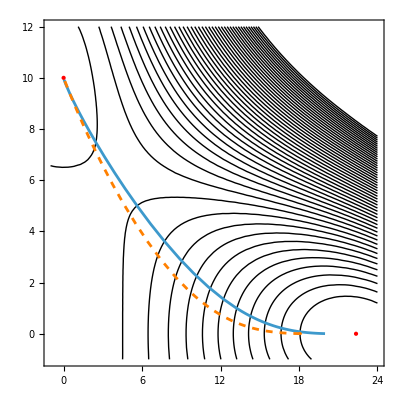

```mathematica
Show[ContourPlot[V2[x,y],{x,-1,24},{y,-1,12},Contours->50,ContourShading->None,Epilog->{Red,PointSize[Large],Point[{tv2,fv2}]}],ParametricPlot[b1[[1]][x],{x,0,0.582}],ParametricPlot[b2[[1]][x],{x,0,0.228},PlotStyle->{Orange,Dashed}]]
```